# Mercury Retrograde and Flight CANCELLATIONS in the USA from Oct 1987 to May 2017 by Renay Oshop

Mercury retrograde is said to be correlated to events of delay, disappointment, and difficulty. 
Question: Does Mercury Retrograde truly correlate to flight delays?

There is full data on all American flights that is available at the following URL!

Specific page for download of this data https : // www.transtats.bts.gov/DL_SelectFields.asp?Table_ID = 236 & DB_Short _Name = On - Time

Collection of data from this site was in the evening of Jul 21, 2017 Mountain Time

```mathematica
Full data at https://www.transtats.bts.gov/
```

```mathematica
months={"Jan","Feb","Mar","Apr","May","Jun","Jul","Aug","Sep","Oct","Nov","Dec"};years={};missing={};
missing=Reap[For[year=2001,year≤2011,year++,
For[monthnum=1,monthnum<=12,monthnum++,
month=months[[monthnum]];
(*element=Import[ToString[year]<>month<>".csv"][[1,1]];*)
If[ Not[FileExistsQ[ToString[year]<>month<>".csv"]],Sow[ToString[year]<>month]](*CHECK*);
];];]
```

{Null,{{2010Jun,2010Jul}}}

NOTE : The June and July 2010 Files were inaccessible in the BTS website. So, I will stop collection in Dec 2009.

## Acquire flight data (month by month)and collate year by year. Note that the major security events of Sept 2001 and their attendant flight cancellations are included in the analysis and were removed as outliers. (Mercury was prograde during this time.)

```mathematica
months={"Jan","Feb","Mar","Apr","May","Jun","Jul","Aug","Sep","Oct","Nov","Dec"};years={};
For[year=1987,year≤1987,year++,
rawyear={};
For[monthnum=10,monthnum≤12,monthnum++,
month=months[[monthnum]];
rawmonth=Import[ToString[year]<>month<>".csv"];(*CHECK*)
rawmonth2=Drop[rawmonth,1][[All,{1,2,3,4}]];
rawmonth3=Table[{rawmonth2[[i,{1,2,3}]],rawmonth2[[i,4]]},{i,1,Length[rawmonth2]}];
monthgathers=GatherBy[rawmonth3,First];
monthavgs=Table[{monthgathers[[i,1,1]],N[Mean[monthgathers[[i,All,2]]]]},{i,1,Length[monthgathers]}];
AppendTo[years,monthavgs]](*CHECK*)
];
For[year=1988,year≤2009,year++,
rawyear={};
For[monthnum=1,monthnum<=12,monthnum++,
month=months[[monthnum]];
rawmonth=Import[ToString[year]<>month<>".csv"];(*CHECK*)
rawmonth2=Drop[rawmonth,1][[All,{1,2,3,4}]];
rawmonth3=Table[{rawmonth2[[i,{1,2,3}]],rawmonth2[[i,4]]},{i,1,Length[rawmonth2]}];
monthgathers=GatherBy[rawmonth3,First];
monthavgs=Table[{monthgathers[[i,1,1]],N[Mean[monthgathers[[i,All,2]]]]},{i,1,Length[monthgathers]}];
AppendTo[years,monthavgs]](*CHECK*)
];
(*For[year=2017,year≤2017,year++,
rawyear={};
For[monthnum=1,monthnum≤5,monthnum++,
month=months[[monthnum]];
rawmonth=Import[ToString[year]<>month<>".csv"];(*CHECK*)
rawmonth2=Drop[rawmonth,1][[All,{1,2,3,4}]];
rawmonth3=Table[{rawmonth2[[i]][[{1,2,3}]],rawmonth2[[i]][[4]]},{i,1,Length[rawmonth2]}];
monthgathers=GatherBy[rawmonth3,First];
monthavgs=Table[{monthgathers[[i,1,1]],N[Mean[monthgathers[[i,All,2]]]]},{i,1,Length[monthgathers]}];
AppendTo[years,monthavgs]](*CHECK*)
];*)
Export["years.mx",years];
```

## Acquire Mercury retrogression data day by day for 30 years and run ANOVA and other tests

```mathematica
years=Import["years.mx"]
```

{{{{1987,10,19},0.00583367},{{1987,10,20},0.00895279},{{1987,10,21},0.0061212},{{1987,10,22},0.00557217},{{1987,10,23},0.00568299},{{1987,10,24},0.00506744},{{1987,10,25},0.00817497},{{1987,10,26},0.00579671},{{1987,10,27},0.00537269},{{1987,10,28},0.011787},{{1987,10,29},0.00526991},{{1987,10,30},0.00473773},{{1987,10,31},0.00982893},{{1987,10,1},0.0103616},{{1987,10,2},0.00515324},{{1987,10,3},0.00664845},{{1987,10,4},0.0078662},{{1987,10,5},0.00901143},{{1987,10,6},0.0063083},{{1987,10,7},0.00263425},{{1987,10,8},0.00337177},{{1987,10,9},0.00385604},{{1987,10,10},0.00499218},{{1987,10,11},0.0032097},{{1987,10,12},0.0246029},{{1987,10,13},0.00733266},{{1987,10,14},0.00452519},{{1987,10,15},0.00316413},{{1987,10,16},0.00512509},{{1987,10,17},0.00708435},{{1987,10,18},0.00377224}},265,{{{2009,12,3},0.00514628},{{2009,12,4},0.0339153},28,{{2009,12,2},0.0116593}}}
 |  |  |  |

```mathematica
years0=Flatten[years,1]
```

{{{1987,10,19},0.00583367},{{1987,10,20},0.00895279},{{1987,10,21},0.0061212},{{1987,10,22},0.00557217},{{1987,10,23},0.00568299},{{1987,10,24},0.00506744},{{1987,10,25},0.00817497},{{1987,10,26},0.00579671},{{1987,10,27},0.00537269},{{1987,10,28},0.011787},{{1987,10,29},0.00526991},{{1987,10,30},0.00473773},{{1987,10,31},0.00982893},{{1987,10,1},0.0103616},{{1987,10,2},0.00515324},{{1987,10,3},0.00664845},{{1987,10,4},0.0078662},8094,{{2009,12,17},0.00631789},{{2009,12,18},0.0216026},{{2009,12,19},0.158524},{{2009,12,20},0.105068},{{2009,12,21},0.0156757},{{2009,12,22},0.0186205},{{2009,12,23},0.0277686},{{2009,12,24},0.0461355},{{2009,12,25},0.0312847},{{2009,12,26},0.0461548},{{2009,12,27},0.0169082},{{2009,12,28},0.00750718},{{2009,12,29},0.0223526},{{2009,12,30},0.00864027},{{2009,12,31},0.0150805},{{2009,12,1},0.00502455},{{2009,12,2},0.0116593}}
 |  |  |  |

```mathematica
years0[[1]]
```

{{1987,10,19},0.00583367}

```mathematica
dates=Table[DateObject[years0[[i,1]],TimeObject[{12,0,0},TimeZone->"America/Chicago"]],{i,1,Length[years0]}];
```

```mathematica
Short[dates,100]
```

{Mon 19 Oct 1987 12:00:00CDT,Tue 20 Oct 1987 12:00:00CDT,Wed 21 Oct 1987 12:00:00CDT,Thu 22 Oct 1987 12:00:00CDT,Fri 23 Oct 1987 12:00:00CDT,Sat 24 Oct 1987 12:00:00CDT,Sun 25 Oct 1987 12:00:00CST,Mon 26 Oct 1987 12:00:00CST,Tue 27 Oct 1987 12:00:00CST,Wed 28 Oct 1987 12:00:00CST,Thu 29 Oct 1987 12:00:00CST,Fri 30 Oct 1987 12:00:00CST,Sat 31 Oct 1987 12:00:00CST,Thu 1 Oct 1987 12:00:00CDT,Fri 2 Oct 1987 12:00:00CDT,Sat 3 Oct 1987 12:00:00CDT,Sun 4 Oct 1987 12:00:00CDT,Mon 5 Oct 1987 12:00:00CDT,Tue 6 Oct 1987 12:00:00CDT,Wed 7 Oct 1987 12:00:00CDT,776,Mon 14 Dec 2009 12:00:00CST,Tue 15 Dec 2009 12:00:00CST,Wed 16 Dec 2009 12:00:00CST,Thu 17 Dec 2009 12:00:00CST,Fri 18 Dec 2009 12:00:00CST,Sat 19 Dec 2009 12:00:00CST,Sun 20 Dec 2009 12:00:00CST,Mon 21 Dec 2009 12:00:00CST,Tue 22 Dec 2009 12:00:00CST,Wed 23 Dec 2009 12:00:00CST,Thu 24 Dec 2009 12:00:00CST,Fri 25 Dec 2009 12:00:00CST,Sat 26 Dec 2009 12:00:00CST,Sun 27 Dec 2009 12:00:00CST,Mon 28 Dec 2009 12:00:00CST,Tue 29 Dec 2009 12:00:00CST,Wed 30 Dec 2009 12:00:00CST,Thu 31 Dec 2009 12:00:00CST,Tue 1 Dec 2009 12:00:00CST,Wed 2 Dec 2009 12:00:00CST}
 |  |  |  |

```mathematica
Length[dates]
```

8128

```mathematica
flightMerRx=PlanetData[Entity["Planet","Mercury"],EntityProperty["Planet","RetrogradeApparentMotionQuery",{"Date"->#}]]&/@dates;
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

General::stop: Further output of EntityValue::nodat will be suppressed during this calculation.

```mathematica
Export["22 yrs MerRx.mx",flightMerRx]
```

22 yrs MerRx.mx

```mathematica
flightMerRx=Import["22 yrs MerRx.mx"];
```

```mathematica
Length[flightMerRx]
```

8128

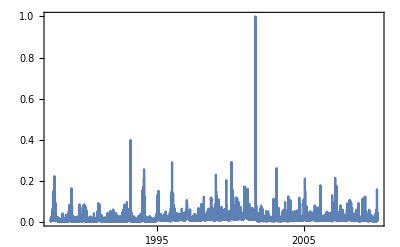

```mathematica
DateListPlot[Transpose[{Delete[dates,pos],Delete[years0[[All,2]],pos]}],PlotRange->All]
```

```mathematica
pos=Position[flightMerRx,_Missing]
```

{{1828},{5603},{5605},{5606},{7694},{7696},{7972}}

```mathematica
;
```

```mathematica
sept11=DateObject[{2001,9,11},TimeObject[{12,0,0},TimeZone->"America/Chicago"]]
```

Tue 11 Sep 2001 12:00:00CDT

```mathematica
pos1=Position[years0[[All,2]],Max[years0[[All,2]]]]
```

{{5095}}

```mathematica
dates[[pos1[[1]]]]
```

{Wed 12 Sep 2001 12:00:00CDT}

```mathematica
pos2=Position[years0[[All,2]],RankedMax[years0[[All,2]],2]]
```

{{5096}}

```mathematica
pos3=Position[years0[[All,2]],RankedMax[years0[[All,2]],3]]
```

{{5094}}

```mathematica
pos4=Position[years0[[All,2]],RankedMax[years0[[All,2]],4]]
```

{{5097}}

```mathematica
pos5=Join[pos,pos1,pos2,pos3,pos4]
```

{{1828},{5603},{5605},{5606},{7694},{7696},{7972},{5095},{5096},{5094},{5097}}

```mathematica
pos5={{1828},{5603},{5605},{5606},{7694},{7696},{7972},{5095},{5096},{5094},{5097}};
```

```mathematica
data=Transpose[{Delete[dates,pos5],Delete[years0[[All,2]],pos5]}]
```

{{Mon 19 Oct 1987 12:00:00CDT,0.00583367},{Tue 20 Oct 1987 12:00:00CDT,0.00895279},{Wed 21 Oct 1987 12:00:00CDT,0.0061212},{Thu 22 Oct 1987 12:00:00CDT,0.00557217},{Fri 23 Oct 1987 12:00:00CDT,0.00568299},{Sat 24 Oct 1987 12:00:00CDT,0.00506744},{Sun 25 Oct 1987 12:00:00CST,0.00817497},{Mon 26 Oct 1987 12:00:00CST,0.00579671},{Tue 27 Oct 1987 12:00:00CST,0.00537269},{Wed 28 Oct 1987 12:00:00CST,0.011787},{Thu 29 Oct 1987 12:00:00CST,0.00526991},8095,{Wed 23 Dec 2009 12:00:00CST,0.0277686},{Thu 24 Dec 2009 12:00:00CST,0.0461355},{Fri 25 Dec 2009 12:00:00CST,0.0312847},{Sat 26 Dec 2009 12:00:00CST,0.0461548},{Sun 27 Dec 2009 12:00:00CST,0.0169082},{Mon 28 Dec 2009 12:00:00CST,0.00750718},{Tue 29 Dec 2009 12:00:00CST,0.0223526},{Wed 30 Dec 2009 12:00:00CST,0.00864027},{Thu 31 Dec 2009 12:00:00CST,0.0150805},{Tue 1 Dec 2009 12:00:00CST,0.00502455},{Wed 2 Dec 2009 12:00:00CST,0.0116593}}
 |  |  |  |

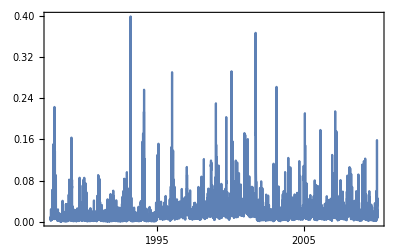

```mathematica
DateListPlot[data,PlotRange->All]
```

```mathematica
Length[flightMerRx]
```

8128

```mathematica
Length[years0]
```

8128

```mathematica
dataretrogrades=Transpose[{Delete[flightMerRx,pos5],Delete[years0[[All,2]],pos5]}]
```

{{retrograde,0.00583367},{retrograde,0.00895279},{retrograde,0.0061212},{retrograde,0.00557217},{retrograde,0.00568299},{retrograde,0.00506744},{retrograde,0.00817497},{retrograde,0.00579671},{retrograde,0.00537269},{retrograde,0.011787},{retrograde,0.00526991},{retrograde,0.00473773},{retrograde,0.00982893},{prograde,0.0103616},{prograde,0.00515324},{prograde,0.00664845},{prograde,0.0078662},{prograde,0.00901143},8082,{prograde,0.00631789},{prograde,0.0216026},{prograde,0.158524},{prograde,0.105068},{prograde,0.0156757},{prograde,0.0186205},{prograde,0.0277686},{prograde,0.0461355},{prograde,0.0312847},{retrograde,0.0461548},{retrograde,0.0169082},{retrograde,0.00750718},{retrograde,0.0223526},{retrograde,0.00864027},{retrograde,0.0150805},{prograde,0.00502455},{prograde,0.0116593}}
 |  |  |  |

```mathematica
data//Short
```

{{Mon 19 Oct 1987 12:00:00CDT,0.00583367},{Tue 20 Oct 1987 12:00:00CDT,0.00895279},{Wed 21 Oct 1987 12:00:00CDT,0.0061212},«8111»,{Thu 31 Dec 2009 12:00:00CST,0.0150805},{Tue 1 Dec 2009 12:00:00CST,0.00502455},{Wed 2 Dec 2009 12:00:00CST,0.0116593}}

```mathematica
Length[data]
```

8117

```mathematica
Export["22 yrs flight cancellation data.mx",dataretrogrades]
```

22 yrs flight cancellation data.mx

```mathematica
bw=GatherBy[Delete[dataretrogrades,pos5],First];
```

```mathematica
LocationTest[{bw[[1,All,2]],bw[[2,All,2]](*,{"TestDataTable",All}}*)},Automatic,{"TestDataTable",All}] (*BUT I DONT THINK A MANN-WHITNEY TEST With MEDIANS IS AS APPROPRIATE*)
```

| Statistic | P-Value
Mann-Whitney | 5.08656×10^6 | 0.779015

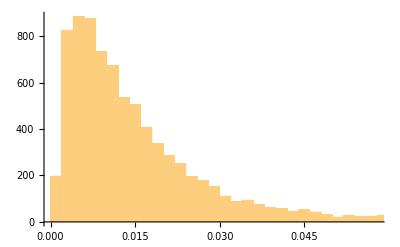

```mathematica
Histogram[dataretrogrades[[All,2]]]
```

```mathematica
FindDistribution[data[[All,2]]]
```

MixtureDistribution[{0.508974,0.491026},{NormalDistribution[-0.0350425,0.0305588],BetaDistribution[2.319,31.0184]}]

```mathematica
standardized=Standardize[Log[data][[All,2]]]; (*Transformation*)
```

```mathematica
Export["22 yrs standardized flight cancellations.mx",standardized]
```

22 yrs standardized flight cancellations.mx

```mathematica
Mean[standardized]
```

-1.80836×10^-14

```mathematica
StandardDeviation[standardized]
```

1.

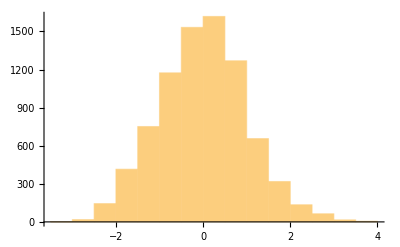

```mathematica
Histogram[standardized]
```

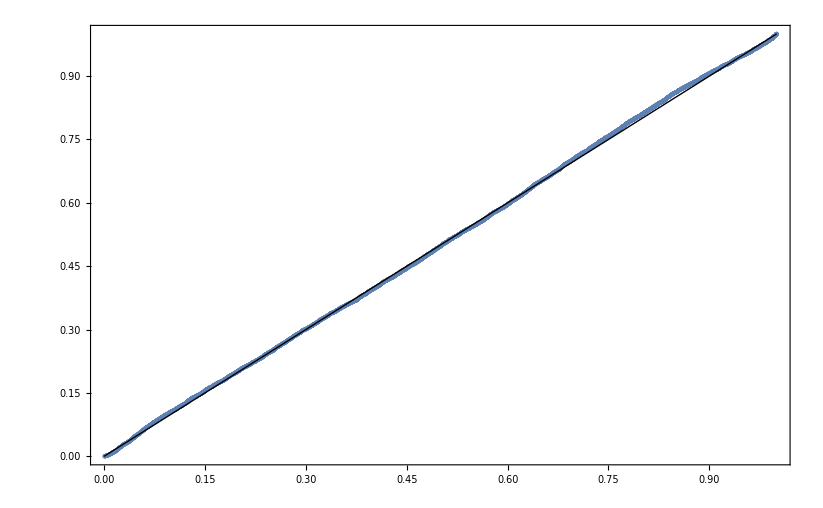

```mathematica
ProbabilityPlot[standardized]
```

```mathematica
Needs["ANOVA`"]
```

```mathematica
Length[standardized]
```

8117

```mathematica
Length[dataretrogrades[[All,1]]]
```

8117

```mathematica
ANOVA[Transpose[{Delete[flightMerRx,pos5],standardized}],PostTests->Bonferroni,CellMeans->True]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 1 | 0.0539149 | 0.0539149 | 0.0539086 | 0.816402
Error | 8115 | 8115.95 | 1.00012 |  | 
Total | 8116 | 8116. |  |  | ,CellMeans→All | -1.80836×10^-14
Model[prograde] | 0.0012486
Model[retrograde] | -0.00531972,PostTests→{Model→Bonferroni | {}}}

```mathematica
Beep[]
```

## Similarly, acquire retrogression data of other planets day by day for 30 years, delete more missing entries, and run ANOVA and other tests

```mathematica
flightVenRx=PlanetData[Entity["Planet", "Venus"],EntityProperty["Planet","RetrogradeApparentMotionQuery",{"Date"->#}]]&/@dates;
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

General::stop: Further output of EntityValue::nodat will be suppressed during this calculation.

```mathematica
Export["22 yr VenRx.mx",flightVenRx];
```

```mathematica
flightMarRx=PlanetData[Entity["Planet","Mars"],EntityProperty["Planet","RetrogradeApparentMotionQuery",{"Date"->#}]]&/@dates;
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

```mathematica
Export["22 yr MarRx.mx",flightMarRx];
```

```mathematica
flightJupRx=PlanetData[Entity["Planet","Jupiter"],EntityProperty["Planet","RetrogradeApparentMotionQuery",{"Date"->#}]]&/@dates;
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

General::stop: Further output of EntityValue::nodat will be suppressed during this calculation.

```mathematica
Export["22 yr JupRx.mx",flightJupRx];
```

```mathematica
flightSatRx=PlanetData[Entity["Planet","Saturn"],EntityProperty["Planet","RetrogradeApparentMotionQuery",{"Date"->#}]]&/@dates;
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

```mathematica
Export["22 yr SatRx.mx",flightSatRx];
```

```mathematica
flightUraRx=PlanetData[Entity["Planet","Uranus"],EntityProperty["Planet","RetrogradeApparentMotionQuery",{"Date"->#}]]&/@dates;
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

General::stop: Further output of EntityValue::nodat will be suppressed during this calculation.

```mathematica
Export["22 yr UraRx.mx",flightUraRx];
```

```mathematica
flightNepRx=PlanetData[Entity["Planet","Neptune"],EntityProperty["Planet","RetrogradeApparentMotionQuery",{"Date"->#}]]&/@dates;
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

General::stop: Further output of EntityValue::nodat will be suppressed during this calculation.

```mathematica
Export["22 yr NepRx.mx",flightNepRx];
```

```mathematica
flightPluRx=MinorPlanetData[Entity["MinorPlanet","Pluto"],EntityProperty["MinorPlanet","RetrogradeApparentMotionQuery",{"Date"->#}]]&/@dates;
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

General::stop: Further output of EntityValue::nodat will be suppressed during this calculation.

```mathematica
Export["22 yr PluRx.mx",flightPluRx];
```

```mathematica
flightMerRx=Import["22 yrs MerRx.mx"];
```

```mathematica
flightVenRx=Import["22 yr VenRx.mx"];
```

```mathematica
flightMarRx=Import["22 yr MarRx.mx"];
```

```mathematica
flightJupRx=Import["22 yr JupRx.mx"];
```

```mathematica
flightSatRx=Import["22 yr SatRx.mx"];
```

```mathematica
flightUraRx=Import["22 yr UraRx.mx"];
```

```mathematica
flightNepRx=Import["22 yr NepRx.mx"];
```

```mathematica
flightPluRx=Import["22 yr PluRx.mx"];
```

```mathematica
fulldata=Table[{flightMerRx[[i]],flightVenRx[[i]],flightMarRx[[i]],flightJupRx[[i]],flightSatRx[[i]],flightUraRx[[i]],flightNepRx[[i]],flightPluRx[[i]],Log[years0[[i,2]]]},{i,1,Length[dates]}];
```

```mathematica
fulldata//Short
```

{{retrograde,prograde,prograde,retrograde,prograde,prograde,prograde,prograde,-5.14411},«8126»,{prograde,prograde,prograde,prograde,prograde,prograde,prograde,prograde,-4.45165}}

```mathematica
pos5={{1828},{5603},{5605},{5606},{7694},{7696},{7972},{5095},{5096},{5094},{5097}};
```

```mathematica
Export["22 yrs flight cancellation full data.mx",fulldata]
```

22 yrs flight cancellation full data.mx

```mathematica
alldeletes=Union[pos5,Position[flightVenRx,_Missing],Position[flightMarRx,_Missing],Position[flightJupRx,_Missing],Position[flightSatRx,_Missing],Position[flightUraRx,_Missing],Position[flightNepRx,_Missing],Position[flightPluRx,_Missing]]
```

{{59},{227},{626},{630},{1036},{1205},{1250},{1746},{1747},{1828},{2081},{2108},{2193},{2194},{2197},{2209},{2552},{2896},{3013},{3016},{3638},{3726},{3854},{3921},{3948},{4262},{4300},{4992},{5094},{5095},{5096},{5097},{5225},{5376},{5603},{5605},{5606},{5627},{5849},{6226},{6994},{7379},{7418},{7458},{7694},{7696},{7805},{7806},{7808},{7809},{7877},{7972},{8037},{8085},{8086}}

```mathematica
Length[alldeletes]
```

55

```mathematica
fulldata=Import["flight cancellation full data.mx"];
```

```mathematica
gb=GatherBy[Delete[fulldata,alldeletes][[All,1]]];ratioMer=N[Length[gb[[1]]]/Length[gb[[2]]]] (*MERCURY RATIO*)
```

0.23497

```mathematica
ratioMer/(1+ratioMer)
```

0.190264

```mathematica
gb=GatherBy[Delete[fulldata,alldeletes][[All,2]]];ratioVen=1/N[Length[gb[[1]]]/Length[gb[[2]]]] (*VENUS RATIO*)
```

0.0791338

```mathematica
ratioVen/(1+ratioVen)
```

0.0733309

```mathematica
gb=GatherBy[Delete[fulldata,alldeletes][[All,3]]];ratioMar=1/N[Length[gb[[1]]]/Length[gb[[2]]]](*MARS RATIO*)
```

0.101815

```mathematica
ratioMar/(1+ratioMar)
```

0.0924068

```mathematica
gb=GatherBy[Delete[fulldata,alldeletes][[All,4]]];ratioJup=N[Length[gb[[1]]]/Length[gb[[2]]]](*JUPITER RATIO*)
```

0.444186

```mathematica
ratioJup/(1+ratioJup)
```

0.307568

```mathematica
gb=GatherBy[Delete[fulldata,alldeletes][[All,5]]];ratioSat=1/N[Length[gb[[1]]]/Length[gb[[2]]]](*SATURN RATIO*)
```

0.545368

```mathematica
ratioSat/(1+ratioSat)
```

0.352905

```mathematica
gb=GatherBy[Delete[fulldata,alldeletes][[All,6]]];ratioUra=1/N[Length[gb[[1]]]/Length[gb[[2]]]](*URANUS RATIO*)
```

0.712558

```mathematica
ratioUra/(1+ratioUra)
```

0.416078

```mathematica
gb=GatherBy[Delete[fulldata,alldeletes][[All,7]]];ratioNep=1/N[Length[gb[[1]]]/Length[gb[[2]]]](*NEPTUNE RATIO*)
```

0.762279

```mathematica
ratioNep/(1+ratioNep)
```

0.432553

```mathematica
gb=GatherBy[Delete[fulldata,alldeletes][[All,8]]];ratioPlu=1/N[Length[gb[[1]]]/Length[gb[[2]]]](*SATURN RATIO*)
```

0.760742

```mathematica
ratioPlu/(1+ratioPlu)
```

0.432057

```mathematica
Needs["ANOVA`"]
```

```mathematica
ANOVA[Delete[fulldata,alldeletes],{Mer,Ven,Mars,Jup,Sat,Ura,Nep,Plu,All},{Mer,Ven,Mars,Jup,Sat,Ura,Nep,Plu},PostTests->Bonferroni,CellMeans->False]
```

LinearModelFit::terms: Only 86 terms are needed to represent all nominal values and continuous basis functions, which is fewer than the total number of nominal terms and continuous basis functions 256. A model for 86 terms of basis functions will be returned.

ANOVA::zerodf: The model contains 170 effects or interactions that have zero degrees of freedom. These terms will be omitted from the ANOVA table.

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Mer | 1 | 0.107259 | 0.107259 | 0.164924 | 0.684674
Ven | 1 | 1.82409 | 1.82409 | 2.80475 | 0.0940248
Mars | 1 | 13.1472 | 13.1472 | 20.2153 | 7.01731×10^-6
Jup | 1 | 0.253395 | 0.253395 | 0.389625 | 0.532514
Sat | 1 | 28.9111 | 28.9111 | 44.4541 | 2.77698×10^-11
Ura | 1 | 132.991 | 132.991 | 204.49 | 8.02599×10^-46
Nep | 1 | 2.11507 | 2.11507 | 3.25217 | 0.0713666
Plu | 1 | 64.9061 | 64.9061 | 99.8008 | 2.31002×10^-23
Mer Ven | 1 | 32.8112 | 32.8112 | 50.4511 | 1.32675×10^-12
Mars Mer | 1 | 0.0709113 | 0.0709113 | 0.109034 | 0.741255
Jup Mer | 1 | 1.32855 | 1.32855 | 2.0428 | 0.152967
Mer Sat | 1 | 2.93171 | 2.93171 | 4.50785 | 0.0337703
Mer Ura | 1 | 0.402571 | 0.402571 | 0.619 | 0.431443
Mer Nep | 1 | 6.76634 | 6.76634 | 10.404 | 0.00126247
Mer Plu | 1 | 1.99862 | 1.99862 | 3.07312 | 0.079635
Mars Ven | 1 | 1.22795 | 1.22795 | 1.88811 | 0.169453
Jup Ven | 1 | 21.051 | 21.051 | 32.3685 | 1.32044×10^-8
Sat Ven | 1 | 68.7036 | 68.7036 | 105.64 | 1.25844×10^-24
Ura Ven | 1 | 0.0575431 | 0.0575431 | 0.0884793 | 0.766127
Nep Ven | 1 | 4.1685 | 4.1685 | 6.40956 | 0.0113698
Plu Ven | 1 | 1.951 | 1.951 | 2.9999 | 0.0833083
Jup Mars | 1 | 49.6621 | 49.6621 | 76.3612 | 2.84563×10^-18
Mars Sat | 1 | 6.85391 | 6.85391 | 10.5387 | 0.00117383
Mars Ura | 1 | 2.90272 | 2.90272 | 4.46327 | 0.0346621
Mars Nep | 1 | 0.212379 | 0.212379 | 0.326557 | 0.567709
Mars Plu | 1 | 56.4254 | 56.4254 | 86.7607 | 1.5559×10^-20
Jup Sat | 1 | 280.117 | 280.117 | 430.713 | 3.17498×10^-93
Jup Ura | 1 | 117.377 | 117.377 | 180.481 | 1.05075×10^-40
Jup Nep | 1 | 18.621 | 18.621 | 28.632 | 8.99515×10^-8
Jup Plu | 1 | 0.291987 | 0.291987 | 0.448965 | 0.502846
Sat Ura | 1 | 109.865 | 109.865 | 168.93 | 3.08964×10^-38
Nep Sat | 1 | 55.8452 | 55.8452 | 85.8686 | 2.43115×10^-20
Plu Sat | 1 | 13.6975 | 13.6975 | 21.0616 | 4.5155×10^-6
Nep Ura | 1 | 43.2696 | 43.2696 | 66.5321 | 3.96732×10^-16
Plu Ura | 1 | 5.58736 | 5.58736 | 8.59121 | 0.00338746
Nep Plu | 1 | 17.6056 | 17.6056 | 27.0706 | 2.01032×10^-7
Jup Mer Ven | 1 | 10.5503 | 10.5503 | 16.2223 | 0.00005685
Mer Sat Ven | 1 | 6.96702 | 6.96702 | 10.7126 | 0.0010686
Mer Ura Ven | 1 | 0.186492 | 0.186492 | 0.286753 | 0.592324
Mer Plu Ven | 1 | 0.176006 | 0.176006 | 0.270629 | 0.602924
Jup Mars Mer | 1 | 2.41459 | 2.41459 | 3.71271 | 0.0540349
Mars Mer Sat | 1 | 6.0733 | 6.0733 | 9.33842 | 0.0022514
Mars Mer Ura | 1 | 2.13574 | 2.13574 | 3.28395 | 0.0699978
Mars Mer Nep | 1 | 0.0152989 | 0.0152989 | 0.0235239 | 0.878106
Mars Mer Plu | 1 | 0.877879 | 0.877879 | 1.34984 | 0.24534
Jup Mer Sat | 1 | 11.1898 | 11.1898 | 17.2056 | 0.0000338916
Jup Mer Ura | 1 | 3.40552 | 3.40552 | 5.23639 | 0.0221451
Jup Mer Nep | 1 | 6.02638 | 6.02638 | 9.26627 | 0.00234172
Jup Mer Plu | 1 | 13.1382 | 13.1382 | 20.2015 | 7.06798×10^-6
Mer Sat Ura | 1 | 0.0640079 | 0.0640079 | 0.0984196 | 0.753743
Mer Nep Sat | 1 | 2.35958 | 2.35958 | 3.62814 | 0.0568463
Mer Plu Sat | 1 | 14.4021 | 14.4021 | 22.1449 | 2.57078×10^-6
Mer Nep Ura | 1 | 2.14569 | 2.14569 | 3.29926 | 0.0693487
Mer Plu Ura | 1 | 31.4387 | 31.4387 | 48.3407 | 3.86456×10^-12
Mer Nep Plu | 1 | 0.321823 | 0.321823 | 0.494841 | 0.481796
Jup Sat Ven | 1 | 2.13495 | 2.13495 | 3.28274 | 0.0700495
Jup Ura Ven | 1 | 0.347449 | 0.347449 | 0.534243 | 0.46485
Jup Plu Ven | 1 | 1.84374 | 1.84374 | 2.83496 | 0.0922721
Sat Ura Ven | 1 | 0.585162 | 0.585162 | 0.899755 | 0.342876
Nep Sat Ven | 1 | 0.0331988 | 0.0331988 | 0.051047 | 0.821257
Plu Sat Ven | 1 | 0.352977 | 0.352977 | 0.542744 | 0.461319
Plu Ura Ven | 1 | 3.56037 | 3.56037 | 5.47449 | 0.0193205
Mars Sat Ura | 1 | 4.15444 | 4.15444 | 6.38794 | 0.0115089
Mars Nep Ura | 1 | 0.279782 | 0.279782 | 0.430197 | 0.511911
Mars Plu Ura | 1 | 1.13172 | 1.13172 | 1.74015 | 0.187157
Mars Nep Plu | 1 | 9.28299 | 9.28299 | 14.2737 | 0.000159208
Jup Sat Ura | 1 | 72.4671 | 72.4671 | 111.427 | 7.06109×10^-26
Jup Nep Sat | 1 | 0.155162 | 0.155162 | 0.23858 | 0.625247
Jup Plu Sat | 1 | 0.0971828 | 0.0971828 | 0.14943 | 0.699091
Jup Plu Ura | 1 | 0.833527 | 0.833527 | 1.28165 | 0.257627
Nep Sat Ura | 1 | 3.01789 | 3.01789 | 4.64036 | 0.0312583
Plu Sat Ura | 1 | 16.7719 | 16.7719 | 25.7888 | 3.89509×10^-7
Nep Plu Ura | 1 | 0.450202 | 0.450202 | 0.692238 | 0.405429
Jup Mer Ura Ven | 1 | 8.09191 | 8.09191 | 12.4423 | 0.000422083
Jup Mer Plu Ven | 1 | 0.24732 | 0.24732 | 0.380283 | 0.537469
Mer Sat Ura Ven | 1 | 0.020441 | 0.020441 | 0.0314305 | 0.859288
Mars Mer Plu Ura | 1 | 0.455824 | 0.455824 | 0.700884 | 0.402512
Jup Mer Sat Ura | 1 | 2.90743 | 2.90743 | 4.47052 | 0.0345155
Jup Mer Nep Sat | 1 | 10.71 | 10.71 | 16.4679 | 0.0000499523
Jup Mer Plu Sat | 1 | 0.0340522 | 0.0340522 | 0.0523592 | 0.819014
Jup Mer Plu Ura | 1 | 0.218914 | 0.218914 | 0.336606 | 0.561811
Mer Plu Sat Ura | 1 | 5.08792 | 5.08792 | 7.82328 | 0.00517009
Jup Plu Ura Ven | 1 | 0.312924 | 0.312924 | 0.481157 | 0.487919
Plu Sat Ura Ven | 1 | 0.792805 | 0.792805 | 1.21903 | 0.269584
Jup Plu Sat Ura | 1 | 1.62354 | 1.62354 | 2.49639 | 0.114147
Error | 7987 | 5194.4 | 0.650357 |  | 
Total | 8072 | 6622.35 |  |  | ,PostTests→{Mer→Bonferroni | {},Ven→Bonferroni | {},Mars→Bonferroni | {prograde,retrograde},Jup→Bonferroni | {},Sat→Bonferroni | {prograde,retrograde},Ura→Bonferroni | {prograde,retrograde},Nep→Bonferroni | {prograde,retrograde},Plu→Bonferroni | {prograde,retrograde}}}

```mathematica
gb=GatherBy[Delete[fulldata,alldeletes][[All,{3,9}]],First];"Mars average "<>gb[[1,1,1]]<>"/ average "<>gb[[2,1,1]]<>"="<>ToString[N[Mean[gb[[1,All,2]]]/Mean[gb[[2,All,2]]]]](*Mars RATIO*)
```

Mars average prograde/ average retrograde=1.033

```mathematica
gb=GatherBy[Delete[fulldata,alldeletes][[All,{4,9}]],First];"Jupiter average "<>gb[[1,1,1]]<>"/ average "<>gb[[2,1,1]]<>"="<>ToString[N[Mean[gb[[1,All,2]]]/Mean[gb[[2,All,2]]]]](*Jupiter RATIO*)
```

Jupiter average retrograde/ average prograde=0.99978

```mathematica
gb=GatherBy[Delete[fulldata,alldeletes][[All,{5,9}]],First];"Saturn average "<>gb[[1,1,1]]<>"/ average "<>gb[[2,1,1]]<>"="<>ToString[N[Mean[gb[[1,All,2]]]/Mean[gb[[2,All,2]]]]](*Saturn RATIO*)
```

Saturn average prograde/ average retrograde=0.969297

```mathematica
gb=GatherBy[Delete[fulldata,alldeletes][[All,{6,9}]],First];"Uranus average "<>gb[[1,1,1]]<>"/ average "<>gb[[2,1,1]]<>"="<>ToString[N[Mean[gb[[1,All,2]]]/Mean[gb[[2,All,2]]]]](*Uranus RATIO*)
```

Uranus average prograde/ average retrograde=0.940846

```mathematica
gb=GatherBy[Delete[fulldata,alldeletes][[All,{7,9}]],First];"Neptune average "<>gb[[1,1,1]]<>"/ average "<>gb[[2,1,1]]<>"="<>ToString[N[Mean[gb[[1,All,2]]]/Mean[gb[[2,All,2]]]]](*Neptune RATIO*)
```

Neptune average prograde/ average retrograde=0.946889

```mathematica
gb=GatherBy[Delete[fulldata,alldeletes][[All,{8,9}]],First];"Pluto average "<>gb[[1,1,1]]<>"/ average "<>gb[[2,1,1]]<>"="<>ToString[N[Mean[gb[[1,All,2]]]/Mean[gb[[2,All,2]]]]](*Neptune RATIO*)
```

Pluto average prograde/ average retrograde=0.953827